```mathematica
Ln=4;
```

P(l<L)

```mathematica
P1[l_,p_]:=(1-p)* p^l
```

P(l=L)

```mathematica
P2[L_,p_]:=p^L
```

Ordered Entropy

```mathematica
EN[L_,p_]:=-(Sum[P1[l,p]*Log[P1[l,p]],{l,0,L-1}]+p^L*Log[p^L])
```

Cyclic Entropy

```mathematica
ENC[p_]:=-(Log[1-p]+p/(1-p)*Log[p])
```

```mathematica
h[τ_]:=1/(1+1/τ)
```

```mathematica
T2=Evaluate@Table[P1[i,h[0.5]],{i,0,50}];
T3=Evaluate@Table[P1[i,h[2]],{i,0,50}];
T4=Evaluate@Table[P1[i,h[20]],{i,0,50}];
```

```mathematica
N[Sum[T2[[i]],{i,1,51}]]
N[Sum[T3[[i]],{i,1,51}]]
N[Sum[T4[[i]],{i,1,51}]]
```

1.

1.

0.916949

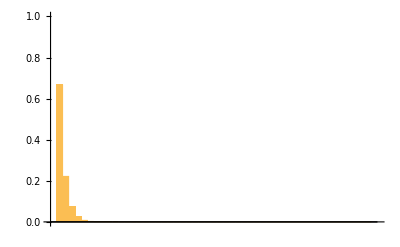

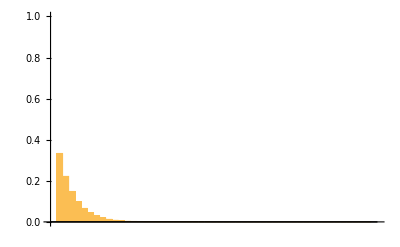

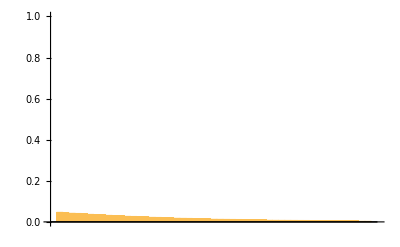

```mathematica
BarChart[T2, PlotRange->{0,1}]
BarChart[T3,PlotRange->{0,1}]
BarChart[T4,PlotRange->{0,1}]
```